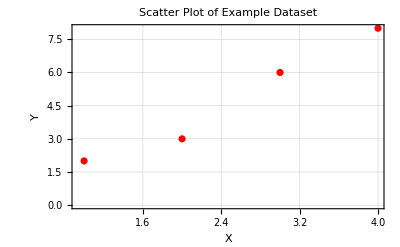

```mathematica
(*Example 1 Data*)X={1,2,3,4};
Y={2,3,6,8};

ListPlot[Transpose[{X,Y}],PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Scatter Plot of Example Dataset"]
```

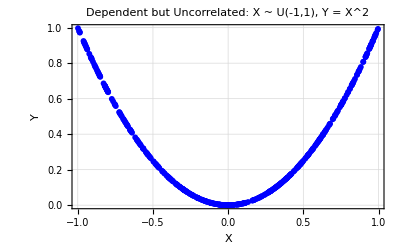

```mathematica
(*Example 2:Zero correlation but dependent*)SeedRandom[0];
n=500;

X2=RandomVariate[UniformDistribution[{-1,1}],n];
Y2=X2^2;

ListPlot[Transpose[{X2,Y2}],PlotStyle->Blue,PlotRange->All,PlotTheme->"Scientific",AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Dependent but Uncorrelated: X ~ U(-1,1), Y = X^2",PlotMarkers->{Automatic,6}]
```